```mathematica
With[{r0=0.1,x0=1.6,y0=0.135,r1=0.712,x1=2.5-3/16-1/4,y1=3/8-0.712,r2=3/16,x2=2.5-3/16,y2=3/16},
Module[{xleft,xright,yleft,dx,dy,dr,c,s},
dx=x1-x0;dy=y1-y0;dr=r1-r0;
c=(-dy dr+dx Sqrt[dx^2-dr^2+dy^2])/(dx^2+dy^2);s=√(1-c^2);
xleft=x0-s r0;yleft=y0+c r0;xright=x1-s r1;
f[x_]:=Piecewise[{
{Indeterminate,x<1.5},
{Sqrt[r0^2-(x-x0)^2]+y0,x<xleft},
{(x-xleft)s/c+yleft,x<xright},
{√(r1^2-(x-x1)^2)+y1,x<x1},
{0.375,x<x2},
{√(r2^2-(x-x2)^2)+y2,x<2.5},{Indeterminate,True}
}]
]
]
```

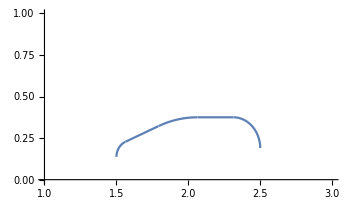

```mathematica
Plot[f[x],{x,1,3},AspectRatio->Automatic,PlotRange->{{1,3},{0,1}}]
```

```mathematica
Solve[{s/c==(dy+c dr)/(dx-s dr),s^2+c^2==1},{c,s}]
```

{{c→(-dr dy-√(-dr^2 dx^2+dx^4+dx^2 dy^2))/(dx^2+dy^2),s→(dr-(dr dy^2)/(dx^2+dy^2)-(dy √(-dx^2 (dr^2-dx^2-dy^2)))/(dx^2+dy^2))/dx},{c→(-dr dy+√(-dr^2 dx^2+dx^4+dx^2 dy^2))/(dx^2+dy^2),s→(dr-(dr dy^2)/(dx^2+dy^2)+(dy √(-dx^2 (dr^2-dx^2-dy^2)))/(dx^2+dy^2))/dx}}

```mathematica
m=Integrate[4π ρ r f[r],{r,1.5,2.5}]
```

8.39318 ρ

```mathematica
solRho=Solve[m==30,ρ]
```

{{ρ→3.57433}}

```mathematica
(* That's grams/in^3 *)
```

```mathematica
ρ/2.54^3/.solRho[[1,1]]
```

0.218119

```mathematica
vol=m/ρ 2.54^3
```

137.54

```mathematica
(* in cm^3 *)
```

```mathematica
moment=Integrate[4π ρ r f[r] r^2,{r,1.5,2.5}]
```

36.4489 ρ

```mathematica
moment 2.54^2/.solRho[[1,1]]
```

840.517

```mathematica
30/2(2.5^2+1.5^2)2.54^2
```

822.579

```mathematica
UnitConvert[Quantity[175,"ounce inch"],"Newtons meters"]//N
```

1.23577 m N

```mathematica
UnitConvert[Quantity[340,"RPM"],"Radians/second"]
```

Quantity::compat: Revolutions/Minutes and Radians/Seconds are incompatible units

$Failed

```mathematica
340 2π /60 // N
```

35.6047

```mathematica
UnitConvert[Quantity[16,"feet"],"Meters"]//N
```

4.8768 m

```mathematica
(* Desire range of 5 meters *)
muzzleVelocity=Sqrt[5 9.8]  (* m/s *)
```

7.

```mathematica
(* Need rω of twice that, assuming perfect speedup *)
rShooterWheel = 2 0.0254;
ωShooterWheel = 2 muzzleVelocity/rShooterWheel
```

275.591

```mathematica
rpmShooterWheel=ωShooterWheel /(2π)60
```

2631.7

```mathematica
gearRatio=20 340/rpmShooterWheel
```

2.58389

```mathematica
4 4 / gearRatio
```

6.19223

```mathematica
(* 6 inch shooter wheel with 4:1 gearing *)
```

```mathematica
rRing = 2.5 0.0254;
ωRing = muzzleVelocity/rRing
```

110.236

```mathematica
rpmRing=ωRing/(2π)60
```

1052.68